```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];Get["HopfE`"];
(*Latex dictionary*)
Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[th1]:=Subscript[θ,1];Format[th2]:=Subscript[θ,2];Format[thv]:=Subscript[θ,v];
Format[th]:=θ;
Format[La]:=Λ;Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[bev]:=Subscript[β,v];
Format[v1]:=Subscript[v,1];
Format[al1]:=Subscript[α,1];Format[al2]:=Subscript[α,2];Format[alv]:=Subscript[α,v];Format[si]:=σ;Format[rh]:=ρ;
Format[si1]:=Subscript[σ,1];Format[si2]:=Subscript[σ,2];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[y1]:=Subscript[y,1];Format[y2]:=Subscript[y,2];
Format[r1]:=Subscript[r,1];Format[r2]:=Subscript[r,2];
Format[c1]:=Subscript[c,1];Format[c2]:=Subscript[c,2];
RN={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"->"v1","v1"+"i2"->2"i2","s"->0,"v1"->0,"i1"->0,"i2"->0};

rts={La,be1*s*i1,be2*s*i2,rh *s,bev*v1*i2,mu*s,mu*v1,(mu+ga1)*i1,(mu+ga2)*i2};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
(*Get bdAn outputs*)
{RHS,var,par, cp,mSi,Jx,Jy,E0,ngm,R0,R0A,EA,E1t,E2t} = bdAn[RN, rts];
Print["R1,R2 are",{R01,R02}=R0A/.E0," R21 is",R21=R0A[[2]]/.E1t[[1]]]
```

reactions and transitions: (0→s | Λ
i1+s→2 i1 | β_1 i_1 s
i2+s→2 i2 | β_2 i_2 s
s→v1 | ρ s
i2+v1→2 i2 | β_v i_2 v_1
s→0 | μ s
v1→0 | μ v_1
i1→0 | i_1 (γ_1+μ)
i2→0 | i_2 (γ_2+μ))

RHS=(Λ-β_1 i_1 s-β_2 i_2 s-μ s-ρ s
-i_1 (γ_1+μ)+β_1 i_1 s
-i_2 (γ_2+μ)+β_2 i_2 s+β_v i_2 v_1
ρ s-β_v i_2 v_1-μ v_1) has var {s,i_1,i_2,v_1} par{β_1,β_2,β_v,γ_1,γ_2,Λ,μ,ρ}

minimal siphons {{i1},{i2}} and invasion species are at positions: {2,3}

DFE solution E0: {s→Λ/(μ+ρ),v_1→(Λ ρ)/(μ (μ+ρ)),i_1→0,i_2→0}

NGM K= ((β_1 s)/(γ_1+μ) | 0
0 | (β_2 s+β_v v_1)/(γ_2+μ))

Raw eigenvalues: {(β_1 s)/(γ_1+μ),(β_2 s+β_v v_1)/(γ_2+μ)}

Raw eigenvectors: {{1,0},{0,1}}

Strain positions - strain 1: {2}, strain 2: {3}

Eigenvector 1: {1,0} -> Eigenvalue 1: (β_1 s)/(γ_1+μ)

Eigenvector 2: {0,1} -> Eigenvalue 2: (β_2 s+β_v v_1)/(γ_2+μ)

Final ordering decision: eigenvals in original order

Ordered reproduction functions R0A: {(β_1 s)/(γ_1+μ),(β_2 s+β_v v_1)/(γ_2+μ)}

R0A[[1]] (strain 1): (β_1 s)/(γ_1+μ)

R0A[[2]] (strain 2): (β_2 s+β_v v_1)/(γ_2+μ)

Number of boundary systems= 2; first sys has 2 sols, second sys has 3 sols

E1t solutions:

1: {i_1→(β_1 Λ-γ_1 μ-μ^2-γ_1 ρ-μ ρ)/(β_1 (γ_1+μ)),s→(γ_1+μ)/β_1,v_1→((γ_1+μ) ρ)/(β_1 μ)}

2: {i_1→0,s→Λ/(μ+ρ),v_1→(Λ ρ)/(μ (μ+ρ))}

E2t solutions:

1: {i_2→0,s→Λ/(μ+ρ),v_1→(Λ ρ)/(μ (μ+ρ))}

2: {i_2→-1/(2 β_2 β_v (γ_2+μ))(-β_2 β_v Λ+β_2 γ_2 μ+β_v γ_2 μ+β_2 μ^2+β_v μ^2+β_v γ_2 ρ+β_v μ ρ-√(-4 (-β_2^2 μ+β_2 β_v μ) (β_v γ_2 Λ+β_v Λ μ)+(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ)^2)),s→1/(2 β_2 (β_2-β_v) μ)(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ+√(-4 (-β_2^2 μ+β_2 β_v μ) (β_v γ_2 Λ+β_v Λ μ)+(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ)^2)),v_1→-1/(2 (β_2-β_v) β_v μ)(-β_2 β_v Λ-β_2 γ_2 μ+β_v γ_2 μ-β_2 μ^2+β_v μ^2-β_v γ_2 ρ-β_v μ ρ+√(-4 (-β_2^2 μ+β_2 β_v μ) (β_v γ_2 Λ+β_v Λ μ)+(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ)^2))}

3: {i_2→-1/(2 β_2 β_v (γ_2+μ))(-β_2 β_v Λ+β_2 γ_2 μ+β_v γ_2 μ+β_2 μ^2+β_v μ^2+β_v γ_2 ρ+β_v μ ρ+√(-4 (-β_2^2 μ+β_2 β_v μ) (β_v γ_2 Λ+β_v Λ μ)+(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ)^2)),s→1/(2 β_2 (β_2-β_v) μ)(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ-√(-4 (-β_2^2 μ+β_2 β_v μ) (β_v γ_2 Λ+β_v Λ μ)+(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ)^2)),v_1→-1/(2 (β_2-β_v) β_v μ)(-β_2 β_v Λ-β_2 γ_2 μ+β_v γ_2 μ-β_2 μ^2+β_v μ^2-β_v γ_2 ρ-β_v μ ρ-√(-4 (-β_2^2 μ+β_2 β_v μ) (β_v γ_2 Λ+β_v Λ μ)+(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ)^2))}

R1,R2 are{(β_1 Λ)/((γ_1+μ) (μ+ρ)),((β_2 Λ)/(μ+ρ)+(β_v Λ ρ)/(μ (μ+ρ)))/(γ_2+μ)} R21 is((β_2 (γ_1+μ))/β_1+(β_v (γ_1+μ) ρ)/(β_1 μ))/(γ_2+μ)

```mathematica
{E1,E2,R12,R21,coP,fl}=invN[E1t,E2t,R0A,E0,par,cp,1,2];
coP
```

Selected E1 (solution 1): {i_1→(β_1 Λ-γ_1 μ-μ^2-γ_1 ρ-μ ρ)/(β_1 (γ_1+μ)),s→(γ_1+μ)/β_1,v_1→((γ_1+μ) ρ)/(β_1 μ)}

Selected E2 (solution 2): {i_2→-1/(2 β_2 β_v (γ_2+μ))(-β_2 β_v Λ+β_2 γ_2 μ+β_v γ_2 μ+β_2 μ^2+β_v μ^2+β_v γ_2 ρ+β_v μ ρ-√(-4 (-β_2^2 μ+β_2 β_v μ) (β_v γ_2 Λ+β_v Λ μ)+(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ)^2)),s→1/(2 β_2 (β_2-β_v) μ)(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ+√(-4 (-β_2^2 μ+β_2 β_v μ) (β_v γ_2 Λ+β_v Λ μ)+(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ)^2)),v_1→-1/(2 (β_2-β_v) β_v μ)(-β_2 β_v Λ-β_2 γ_2 μ+β_v γ_2 μ-β_2 μ^2+β_v μ^2-β_v γ_2 ρ-β_v μ ρ+√(-4 (-β_2^2 μ+β_2 β_v μ) (β_v γ_2 Λ+β_v Λ μ)+(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ)^2))}

invasion numbers are {((γ_1+μ) (β_2 μ+β_v ρ))/(β_1 μ (γ_2+μ)),-1/(2 β_2 (β_2-β_v) μ (γ_1+μ))β_1 (β_2 β_v Λ-β_2 γ_2 μ+β_v γ_2 μ-β_2 μ^2+β_v μ^2+β_v γ_2 ρ+β_v μ ρ-√(-4 (-β_2^2 μ+β_2 β_v μ) (β_v γ_2 Λ+β_v Λ μ)+(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ)^2))}

R12 rational: True, R21 rational: False

Step 1: FindInstance with rational constraints only...

Rational constraints: {β_1>0,β_2>0,β_v>0,γ_1>0,γ_2>0,Λ>0,μ>0,ρ>0,(β_1 Λ)/((γ_1+μ) (μ+ρ))>1,((β_2 Λ)/(μ+ρ)+(β_v Λ ρ)/(μ (μ+ρ)))/(γ_2+μ)>1,((γ_1+μ) (β_2 μ+β_v ρ))/(β_1 μ (γ_2+μ))>1}

FindInstance for rational constraints succeeded: {β_1→5,β_2→3,β_v→5/2,γ_1→1,γ_2→1,Λ→1,μ→1,ρ→1}

Step 2: NMinimize with R21 objective: (-5/4-1/(2 β_2 (β_2-β_v) μ (γ_1+μ))β_1 (β_2 β_v Λ-β_2 γ_2 μ+β_v γ_2 μ-β_2 μ^2+β_v μ^2+β_v γ_2 ρ+β_v μ ρ-√(-4 (-β_2^2 μ+β_2 β_v μ) (β_v γ_2 Λ+β_v Λ μ)+(-β_2 β_v Λ+β_2 γ_2 μ-β_v γ_2 μ+β_2 μ^2-β_v μ^2-β_v γ_2 ρ-β_v μ ρ)^2)))^2

Using same constraints as FindInstance: {β_1>0,β_2>0,β_v>0,γ_1>0,γ_2>0,Λ>0,μ>0,ρ>0,(β_1 Λ)/((γ_1+μ) (μ+ρ))>1,((β_2 Λ)/(μ+ρ)+(β_v Λ ρ)/(μ (μ+ρ)))/(γ_2+μ)>1,((γ_1+μ) (β_2 μ+β_v ρ))/(β_1 μ (γ_2+μ))>1}

Starting point for NMinimize: {β_1→5,β_2→3,β_v→5/2,γ_1→1,γ_2→1,Λ→1,μ→1,ρ→1}

Variable ranges for NMinimize: {{β_1,4.9,5.1},{β_2,2.9,3.1},{β_v,2.4,2.6},{γ_1,0.9,1.1},{γ_2,0.9,1.1},{Λ,0.9,1.1},{μ,0.9,1.1},{ρ,0.9,1.1}}

NMinimize completed after 264 steps

NMinimize result: {7.57622×10^-27,{β_1→5.02999,β_2→2.91461,β_v→2.51824,γ_1→0.914693,γ_2→1.03606,Λ→1.13707,μ→0.874319,ρ→0.867067}}

NMinimize succeeded with objective value: 7.57622×10^-27

under coP: {β_1→5.02999,β_2→2.91461,β_v→2.51824,γ_1→0.914693,γ_2→1.03606,Λ→1.13707,μ→0.874319,ρ→0.867067} invasion nrs are {1.00759,1.25} repr nrs are {1.83589,1.84982}

END invNr OUTPUT

{β_1→5.02999,β_2→2.91461,β_v→2.51824,γ_1→0.914693,γ_2→1.03606,Λ→1.13707,μ→0.874319,ρ→0.867067}

Checked 513 potential coexistence points

All Rij equations: {0.36499 β_1==1,0.523457 (1.6307+0.652971 β_2)==1,(1.07109 (2.18349+0.874319 β_2))/β_1==1,-(0.319659 β_1 (8.37744+1.19315 β_2-√((-8.37744-1.19315 β_2)^2-21.8809 (2.20175 β_2-0.874319 β_2^2))))/((-2.51824+β_2) β_2)==1}

All Rij equations: {0.36499 β_1==1,0.523457 (1.6307+0.652971 β_2)==1,(1.07109 (2.18349+0.874319 β_2))/β_1==1,-(0.319659 β_1 (8.37744+1.19315 β_2-√((-8.37744-1.19315 β_2)^2-21.8809 (2.20175 β_2-0.874319 β_2^2))))/((-2.51824+β_2) β_2)==1}

DFE: 140 (2%)

E2: 2369 (40%)

E1: 2937 (49%)

EE-Stable: 513 (9%)

{11.5313,Null}

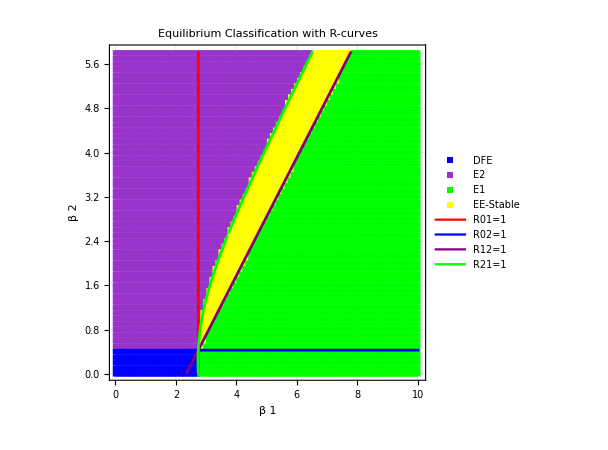

```mathematica
plotInd={1,2};varInd={1,2,3};p0val=par/.coP;steTol=10^(-8);staTol=10^(-10);choTol=10^(-13);(*tMax=300;nIc=8;*)
Timing[{fPl,unC,res}=scan[RHS,var,par,p0val,plotInd,varInd,Automatic,Automatic,steTol,staTol,choTol,R01,R02,R12,R21];]
fPl
```

```mathematica
Export["LiScan.pdf",fPl]
```

LiScan.pdf